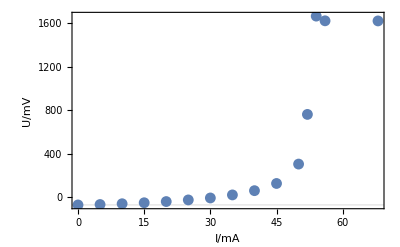

```mathematica
iold = {0, 5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 52, 54, 56, 68};
uold = {-69, -65, -58, -49, -38, -23, -5, 23, 62, 128, 306, 762, 1664, 1621, 1620};
ListPlot[Transpose[{iold, uold}], Frame->True, FrameLabel->{"I/mA", "U/mV"}, GridLines->{{}, {-69}}]
```

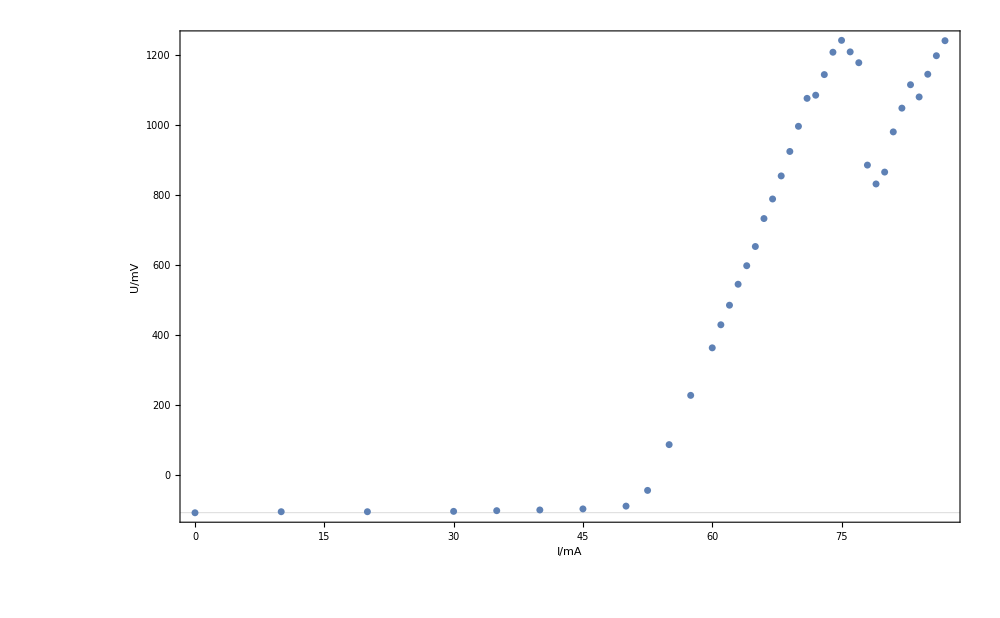

FittedModel[60.2147 (-53.749+x)]

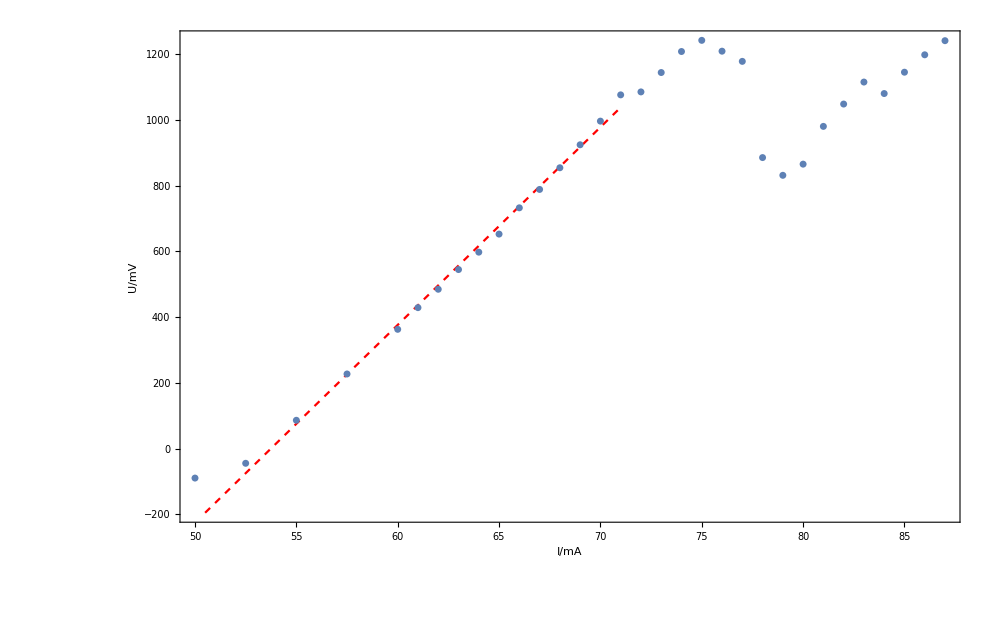

```mathematica
i={0, 10, 20, 30, 35, 40, 45, 50,52.5, 55,57.5, 60,  65, 70, 71, 72, 73, 74, 75, 61, 62, 63, 64, 66, 67, 68, 69, 76, 77, 78, 79, 80, 81, 82, 83, 84, 85, 86, 87};
u={-109, -106, -106, -105, -103, -101, -98, -90, -45, 86,227, 363,  653, 997, 1077, 1086, 1145, 1209, 1243, 429, 485, 545, 598, 733, 789, 855, 925, 1210, 1179, 886, 832, 866, 981, 1049, 1116, 1081, 1146, 1199, 1242};
data = Transpose[{i, u}];
ListPlot[data, Frame->True,Axes->False, FrameLabel->{"I/mA", "U/mV"}, GridLines->{{}, {u[[1]]}}, ImageSize->1000, PlotStyle->{PointSize[0.005]}]
fitdata = Select[data, #[[1]] > 50 && #[[1]]≤ 71&];
nlm = NonlinearModelFit[fitdata, b (x - a), {a, b}, x]
Show[Plot[Normal[nlm], {x, fitdata[[1, 1]] - 2, fitdata[[-1, 1]] + 2}, Frame->True,Axes->False, FrameLabel->{"I/mA", "U/mV"}, PlotRange->{{50, Max[i]}, All}, ImageSize->1000, PlotStyle->{Red, Dashed}], ListPlot[data,  GridLines->{{}, {u[[1]]}}, PlotStyle->{PointSize[0.005]}]]
```